```mathematica
(*IMPOTAR DATOS*)
datos=Import["/Users/miguel/Desktop/Delfín/Mathematica/datos.txt","Table"];
datos // TableForm



vertices={{0,5000,1},{2500,5000,2},{4000,5000,3},{5000,5000,4},{0,3000,5},{2000,3000,6},{2500,3000,7},{4000,2750,8},{5000,2750,9},{2000,2000,10},{2500,2000,11},{3750,2000,12},{4000,2000,13},{5000,2000,14},{3750,1250,15},{5000,1250,16},{0,500,17},{2000,500,18},{0,0,19},{2000,0,20},{3750,0,21},{5000,0,22}};
aristas={{1,2,2500},{2,3,1500},{3,4,1000},{5,6,2000},{6,7,500},{8,9,1000},{10,11,500},{11,12,1250},{12,13,250},{13,14,1000},{15,16,1250},{17,18,2000},{19,20,2000},{20,21,1750},{21,22,1250},{4,9,2250},{9,14,750},{14,16,750},{16,22,1250},{3,8,2250},{8,13,750},{12,15,750},{15,21,1250},{2,7,2000},{7,11,1000},{6,10,1000},{10,18,1500},{18,20,500},{1,5,2000},{5,17,2500},{17,19,500}};
```

10 | 5000 | 5000 | 
2000 | 3000 | 2500 | 2000
4000 | 2750 | 5000 | 2000
0 | 5000 | 2500 | 3000
2500 | 5000 | 4000 | 2000
4000 | 5000 | 5000 | 2750
2000 | 2000 | 3750 | 0
3750 | 2000 | 5000 | 1250
3750 | 1250 | 5000 | 0
0 | 500 | 2000 | 0
0 | 3000 | 2000 | 500
7 |  |  |

Aristas No Dirigidas, Pesos de Aristas y Coordenadas de Vértices

```mathematica
nEdges=Map[#_⟦1⟧<->#_⟦2⟧&,aristas];
```

```mathematica
eWeigth=Map[#_⟦3⟧&,aristas];
```

```mathematica
coord=Map[Take[#,2]&,vertices];
```

Calculo de Cantidad de Aristas y Pesos de Aristas

```mathematica
Length[nEdges];
Length[eWeigth];
Length[coord];
```

Relación de Aristas con sus Pesos

```mathematica
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
```

Construcción del Gráfo a partir de las Aristas, Pesos y Coordenadas

```mathematica
g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges];
```

Generacion de la lista de poligonos

{{0,5000},{2500,5000},{4000,5000},{5000,5000},{0,3000},{2000,3000},{2500,3000},{4000,2750},{5000,2750},{2000,2000},{2500,2000},{3750,2000},{4000,2000},{5000,2000},{3750,1250},{5000,1250},{0,500},{2000,500},{0,0},{2000,0},{3750,0},{5000,0}}

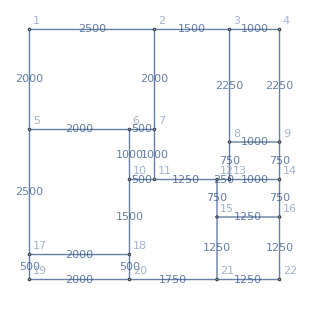

{{6<->10,10<->11,11<->7,7<->6},{8<->13,13<->14,14<->9,9<->8},{1<->5,5<->6,6<->7,7<->2,2<->1},{2<->7,7<->11,11<->12,12<->13,13<->8,8<->3,3<->2},{3<->8,8<->9,9<->4,4<->3},{10<->18,18<->20,20<->21,21<->15,15<->12,12<->11,11<->10},{12<->15,15<->16,16<->14,14<->13,13<->12},{15<->21,21<->22,22<->16,16<->15},{17<->19,19<->20,20<->18,18<->17},{5<->17,17<->18,18<->10,10<->6,6<->5}}

```mathematica
listaDeVertices = VertexList[g];
(*LISTA DE COORDENADAS DE LOS VERTICES DEL GRAFO*)
coordenadas=GraphEmbedding[g]
g

(*VARIABLES AUXILIARES*)
poligonos={};
vertice1 =0;
(*COORDENADAS DEL VERTICE SUPERIOR IZQUIERDO*)
coorx1=0;
coorx2 =0;
vertice2 =0;
(*COORDENADAS DEL VETICE INFERIOR DERECHO*)
coory1=0;
coory2=0;
vertice3 =0;
vertice4=0;
(*VARIABLE PARA CONSTRUIR EL POLIGONO*)
poligonInd={};
(*AUXILIAR DE VERTICE*)
auxiliar=0;

(*SE RECORREN LAS FILAS DEL ARCHIVO IMPORTADO SALTANDO LA FILA 1*)
For[i=2, i<Length[datos], i++,
(*LA VARIABLE DEL POLIGONO SE LIMPIA*)
poligonInd={};
(*SE DIVIDE EL PROCESO EN DOS, PARA CADA VERTICE EN LA FILA(CADA FILA TIENE 2 VERTICES)*)
For[j=1, j≤ 2, j++,
(*SI ES EL PRIMER CICLO, SE PROCESA EL PRIMER VERTICE*)
If[j==  1,
(*SE OBTIENE EL VERTICE DEL GRAFO QUE CORRESPONDA CON LAS COORDENADAS DADAS EN EL ARCHIVO IMPORTADO*)
vertice1 =Position[coordenadas,{datos[[i]][[1]],datos[[i]][[2]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL VERTICE*)
coorx1 =datos[[i]][[1]];
coory1= datos[[i]][[2]];
,
(*SI ES EL SEGUNDO CICLO, SE PROCESA EL SEGUNDO VERTIDE DE LA FILA DEL ARCHIVO IMPORTADO*)
(*SE GUARDA EL VERTICE*)
vertice2=Position[coordenadas,{datos[[i]][[3]],datos[[i]][[4]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL SEGUNDO EVRTICE*)
coorx2 = datos[[i]][[3]];
coory2= datos[[i]][[4]];
];

];
(*UNA VEZ SE TIENEN LOS VERTICES Y SUS RESPECTIVAS COORDENADAS...*)
(*SE CALCULAN LOS OTROS VERTICES DEL RECTANGULO CON LA MEZCLA DE LAS COORDENADAS DE LOS VERTICES ANTERIORES*)
vertice3 = Position[coordenadas,{coorx1,coory2}][[1]][[1]];
vertice4 = Position[coordenadas,{coorx2,coory1}][[1]][[1]];


(*SE PROCESA EL RECTANGULO PARA ENCONTRAR VERTICES INTERMEDIOS QUE FORMAN PARTE DEL POLIGONO*)
(*EL PROCESO SE REALIZA EN SENTIDO CONTRARIO A LAS MANECILLAS DEL RELOJ, INICIANDO CON EL VERTICE 1, SEGUIDO DEL 3, DEL 4 Y DEL 2*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL IZQUIERDA*)
auxiliar = vertice1;
(*SE RECORREN LAS COORDENADAS DE LOS VERTICES DEL GRAFO*)
For[k =1, k≤Length[coordenadas],k++,
(*SI HORIZONTALMENTE SE ENCUENTRA EN LA POSICION DEL PRIMER VERTICE, SE VERIFICA QUE ESTE ENTRE EL VERTICE 1 Y 3*)
If[coordenadas[[k]][[1]]==  coorx1 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
(*SE CONECTA ESTE VERTICE CON EL ANTERIOR Y SE AGREGA A LA VARIABLE POLIGONO*)
AppendTo[poligonInd,auxiliar<->k ];
(*EL AUXILIAR SE CONVIERTE EN EL ULTIMO VERTICE*)
auxiliar = k;
]
];
(*SE CONECTA EL ULTIMO VERTICE CON EL VERTICE 3*)
AppendTo[poligonInd,auxiliar<->vertice3];



(*EL PROCESO ANTERIOR SE REPITE EN LOS LADOS RESTANTES*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL INFERIOR*)
auxiliar = vertice3;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory2 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice2];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL DERECHA*)
auxiliar = vertice2;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[1]]==  coorx2 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice4];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL SUPERIOR*)
auxiliar = vertice4;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory1 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice1];
AppendTo[poligonos,poligonInd]
]

(*LA VARIABLE FINAL CONTIENE LA LISTA DE LOS POLIGONOS*)
poligonos
```